```mathematica
ClearAll;
Clear[na];
sel[au_,kl_]:=au[[All,kl]];
(*
Comenzamos con la definicion de ferm, que genera el espacio de Fock para na SP states de un fermion (Dim(H) = 2^na estados puros). No usamos Module, ya que muchas de las definciones las usaremos por fuera del entorno de la funcion
*)
ferm[na_]:=(n=na;
Clear[cm,estado,a,v,mat,au,kel];
(*
Table es un análogo a los list comprehension, iterando con {index, start=1, end, paso=1}. IntegerDigits da una representación en base 2 de k, usando n digitos, en formato de lista. Cada uno de estos, representa un estado puro en el espacio de Fock, con cada posición en la tabla el número de ocupación del SP. De este modo, state corresponde a una base del espacio
*)
state=Table[IntegerDigits[k,2,n],{k,0,2^n-1,1}]; 
(* 
Genera una lista de 2^n elementos ceros, salvo el primero. Usa la misma indexacion que state, de modo que indica cual es el vacio del espacio de Fock en la base state
*)
vacio=Table[If[i==1,1,0],{i,Length[state]}];
(* 
Vamos a crear las matrices de destrucción y creación notadas como cm[i]->Subscript[c, i] y cdm[i]->Subscript[c, i]^†, definidas en 2^n x2^n. Para ello, creamos la funcion auxiliar c(i,m), que, dado el indice del elemento de la base (m), y el nivel SP a desocupar (i), devuelve el indice del estado m con el nivel i desocupado, o 0 si ese nivel estaba desocupado (0 ≠ vacio). Además, este índice cuenta con un signo según la paridad de los niveles ocupados previos al i.
*)
c[i_,m_]:=(st=state[[m]];If[st[[i]]==0,0,(-1)^(Tr[Take[st,i-1]])*(FromDigits[ReplacePart[st,i->0],2]+1)]);
(*
Creamos cada una de las matrices de destrucción iterando con Do sobre los niveles de ocupación (i). Para construir cada una de ellas usamos una SparseArray. Notar que las entradas dt=c[i,m]
{If[dt≠0,Abs[dt],m],m}->Sign[dt]}
Indican que el estado m debe ser enviado a Abs[c[i,m]],   con el signo dado para que las relaciones de conmutación sean las correctas (en particular, las relativas al intercambio de dos fermiones). También creamos los op de creacion, trasponiendo los de destrucción
*)
Do[cm[i]=SparseArray[Join[Table[{m,m}->0,{m,Length[state]}],Table[{dt=c[i,m];If[dt≠0,Abs[dt],m],m}->Sign[dt],{m,Length[state]}]]];
cdm[i]=Transpose[cm[i]],{i,n}]; 
(* Generamos los operadores producto Subscript[c, i]^†Subscript[c, j] Subscript[c, i] Subscript[c, j]^† Subscript[c, i] Subscript[c, j] Subscript[c, i]^†Subscript[c, j]^† *)
Do[cdcm[i,j]=cdm[i].cm[j];ccdm[i,j]=cm[i].cdm[j];ccm[i,j]=cm[i].cm[j];cdcd[i,j]=cdm[i].cdm[j],{i,n},{j,n}]; 
(* 
A continuacion, definimos algunas funciones auxiliares
 *) 
 mf[au_]:=MatrixForm[au]; (* Atajo de MatrixForm *)
indx[au_]:=Flatten[SparseArray[au]["NonzeroPositions"],1];
(* Indica las posiciones de los elementos no nulos de un vector au *)
Do[statex[kel]=Select[state,Tr[#]==kel&];leme[kel]=Length[statex[kel]],{kel,0,n,1}];
(* Selecciona estados con kel fermiones para todo kel (kel es el numero de fermiones), almacenado en statex. Mientras que leme[kel] devuelve en numero de estados con esa cantidad de fermiones *) 
Clear[i,j,m,nuu,au];
(*
Vamos a ver ahora las descomposiciones bipartitas de los estados. Estos corresponden a la matrix Γ del paper definida en la ec 9. i corresponde al índice en el espacio de estados de m fermiones, y j al mismo en nuu-m. au es el estado a descomponer. 
Para la eleccion i,j, si creo un estado no nulo (ax.ay==0), tomo el coeficiente de au asociado a ese estado. Adicionalmente, le pongo un signo para BD.
nuu corresponde al numero de particulas, y au el estado a descomponer
*)
cof[i_,j_,m_,nuu_,au_]:=(ax=statex[m][[i]];axi=indx[ax];ay=statex[nuu-m][[j]];
If[ax.ay==0,au[[iex=FromDigits[ax+ay,2]+1]]*(-1)^(Sum[Tr[Take[ay,axi[[ki]]-1]],{ki,Length[axi]}]),0]);
(* Con los coef de Γ, calculamos la matrix de M cuerpos *)
rhomc[m_,nuu_,au_]:= Table[Sum[cof[i,k,m,nuu,au]Conjugate[cof[j,k,m,nuu,au]],{k,leme[nuu-m]}],{i,leme[m]},{j, leme[m]}];
rho1c[v_]:=Table[v.cdcm[j,i].v,{i,n},{j,n}];
(* Calcula la matriz densidad de un cuerpo en el estado v*) 
num=Sum[cdcm[i,i],{i,n}]);

(* operador numero de fermiones *)
ssp[mat_]:=(zp=Eigenvalues[mat];a=Select[zp,#>0&&#<1&];If[Length[a]>0,-(a.Log[a]+(1-a).Log[1-a])/Log[2],0]);
(* Calcula la entropia fermionica de una matriz densidad de un cuerpo mat *)  
rev[au_]:=(let=Length[au];
Table[au[[let-i+1,let-j+1]],{i,let},{j,let}]);
(* reversa del orden de estados *)
```

### Ejemplos

```mathematica
ferm[8];
estat=cdm[1].cdm[2].cdm[3].cdm[4].vacio;
{estat.estat,estat.num.estat,estat}
 m=2;nume=4;
rhomc[m, nume, estat] // mf
m=2; nume=4;cmat=Table[cof[i,j,m,nume,estat],{i,leme[m]},{j,leme[nume-m]}];cmatt=rev[cmat.Transpose[cmat]];cmatt//mf
```

{1,4,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Hamiltoniano de Pairing

Apliquemos ahora el formalismo anterior para estudiar las descomposiciones y matrices de M cuerpos para estados un poco más interesantes. En este caso, evaluaremos los autoestados del hamiltoniano de Pairing. El mismo, consiste en un término de niveles discretos con degeneración dos (por ejemplo, k y k’), junto con otro término que acopla estos dos niveles, reduciendo la energía. De este modo, esperamos que en el fundamental los estados se den únicamente de a pares. Estudiaremos sistemas de 2n estados y n fermiones (porque es donde se da la física más interesante). Construimos el hamiltoniano para n fermiones:

```mathematica
pairing[n_]:=(nn=n;
it=0;
Clear[xst,xstt,indax];
(* Al igual que en ferm, vamos a representar estados usando vectores binarios, que indican los niveles ocupados. En este
caso, vamos a notarlos como (Subscript[k, 1],Subscript[k, 1]'...), de modo que únicamente nos quedamos con los estados con ambas degeneraciones ocupadas,
ya que esperamos que solo estos contribuyan al fudamental. Más aún, para reducir la dimension del espacio, colapsamos la degeneracion, notando los estados como (Subscript[k, 1],Subscript[k, 2]...=(Subscript[k, 1],Subscript[k, 1]',Subscript[k, 2],Subscript[k, 2]'... *)
(* Construimos los estados al igual que en ferm, y nos quedamos unicamente con los estados con n/2 fermiones, ie, estados = statex[n/2]*)
Table[xstate=IntegerDigits[k,2,nn];If[Tr[xstate]==nn/2,it=it+1;xst[it]=xstate;indax[xstate]=it],{k,0,2^nn-1,1}];
itm=it;
Do[xstl[l]=Table[xst[k][[l]],{k,itm}],{l,nn}];
estados=Table[xst[it],{it,itm}];
(* Construimos la parte de la energia de cada nivel *)
e=1.;
e0=e*Table[k-nn/2-1/2,{k,nn}]; (* Energia de cada modo *)
h0=Table[e0.estados[[i]],{i,itm}]; (* Energia de cada estado *)
h00=DiagonalMatrix[h0]; (* Primera parte del Hamiltoniano *)
(* Ahora vamos a construir el término de interacción. Como la constante es la misma, y estamos sumando sobre todos los operadores,
esta simplemente aporta un término G por cada par de estados que difieren en un modo (es decir, que se obtienen via intercambio de las ocupaciones de k <-> k' *)
Clear[g];
hi=Table[If[estados[[i]].estados[[j]]==nn/2-1,g,0],{i,itm},{j,itm}];
h=h00+hi;
(* Definamos ahora una funcion que nos permite pasar de los estados de esta convencion, a la de ferm.
Primero definimos una funcion auxiliar que asigna a que elemento de la base reducida corresponde a la nueva *)
convelem[au_]:=Module[{s=au,x},
x =Table[0,{i,2Length[s]}];
Do[x[[2i-1]]=s[[i]];
    x[[2i]]=s[[i]];,{i,Length[s]}];
x];
conv[au_]:=Module[{s=au, newCor},
state =Table[IntegerDigits[k,2,2 n],{k,0,2^(2n)-1,1}];
newCor = Table[0,{i,Length[state]}];
Do[idx=Position[state,convelem[estados[[k]]]][[1,1]];
newCor[[idx]]=s[[k]],{k,Length[s]}];
newCor];
)
```

Nos interesa ver el comportamiento de los autovalores de la matriz de M cuerpos, para distintos niveles de energía de h (fundamental, primer excitado...) haciendo un barrido en g. Hasta ahora, con pairing, teníamos definido h

```mathematica
d= 12; (* Dimension del espacio *)
M = 1; (* Grado de la descomposicion, donde 0≤M≤d/2 *)
(* Parametros del barrido *)
gmin = 0.1;
gmax = 20;
gstep = 0.1;
ferm[d];
pairing[d/2];
(* Calculamos autovals y autovect de H, y ordenamos de acuerdo al autovalor. El resultado es una lista de la forma
{{autoval,autovect},...}. Como este fue calculado en un subespacio, lo convertimos al espacio original, y finalmente,
calculamos los autovalores de rho *)
eigenTab =ParallelTable[
{evals,evecs}=Eigensystem[h]; 
a=SortBy[Transpose[{evals,evecs}],First];
(* El primer indice de a corresponde al nivel, 1 = fundamental, 2 = 1er excitado... 
Adicionalmente, lo convertimos a la base de ferm *)
targState = conv[a[[1]][[2]]];
(* Calculamos los autovalores de la rhom *)
rhomEvals = Eigenvalues[rhomc[M,d/2,targState]],
{g,gmin,gmax,gstep}];
```

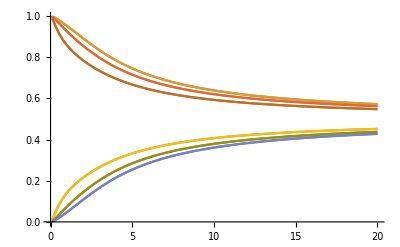

```mathematica
ListLinePlot[Transpose[eigenTab],DataRange->{gmin,gmax}]
```

```mathematica
-Log2[1/2]
```

1